```mathematica
<<CSL`OdeUtils`;
RungeKuttaCatalog[]
x=RungeKuttaCatalog["ode23"];
p=3;
```

Dataset[<>]

```mathematica
RungeKuttaQ[x]
RungeKuttaPairQ[x]
RungeKuttaTableau[x]
RungeKuttaFsalQ[x]
RungeKuttaA[x,p+1]//N
RungeKuttaB[x,p+1]//N
RungeKuttaC[x,p+1]//N
RungeKuttaD[x]//N
RungeKuttaE[x,p+1]//N
```

True

True

0 | 0 | 0 | 0 | 0
1/2 | 1/2 | 0 | 0 | 0
3/4 | 0 | 3/4 | 0 | 0
1 | 2/9 | 1/3 | 4/9 | 0
 | 2/9 | 1/3 | 4/9 | 0
 | 7/24 | 1/4 | 1/3 | 1/8

True

0.0418111

1.34919

1.37721

1.

1.41912

1/6 (6+6 z+3 z^2+z^3)

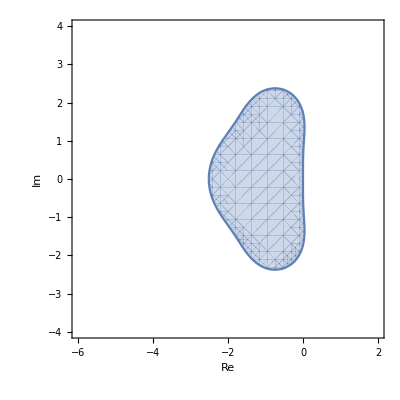

1/6 (6+6 z+3 z^2+z^3)

1

-1/36 y^4 (-3+y^2)

False

True

```mathematica
RungeKuttaLinearStability[x,z]//Simplify
RungeKuttaLinearStabilityPlot[x]
RungeKuttaLinearStabilityP[x,z]//Simplify
RungeKuttaLinearStabilityQ[x,z]//Simplify
RungeKuttaLinearStabilityE[x,y]//Simplify
RungeKuttaAStableQ[x]
RungeKuttaStifflyAccurateQ[x]
```

```mathematica
g=Glm[x,p];
GlmInternalStages[g]
GlmExternalStages[g]
GlmType[g]
```

4

1

1

```mathematica
Dimsim[2,Type->3]
```

<|A→{{0,0},{0,0}},B→{{b_(1,1),b_(1,2)},{b_(2,1),b_(2,2)}},U→{{1,0},{0,1}},V→{{v_1,v_2},{v_1,v_2}},c→{c_1,c_2},W→{{w_(1,0),w_(1,1),w_(1,2)},{w_(2,0),w_(2,1),w_(2,2)}}|>